```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

## a simple k - NN algorithm

```mathematica
BeginPackage["W`KNN`"];
KNN::usage="KNN classifier";

K::usage="number of neighbor";
Distancef::usage="";
```

```mathematica
Begin["`PP`"];
```

```mathematica
Options[KNN]={K->4,Distancef->EuclideanDistance};
(*KNN classifier*)
(*data,temp and tg should all flattened first*)
(*tg also has (0,1) form*)(*the result group is a (0,1) confusion matrix which can use 2-class VF, but Knn chooses only one class for each data, so FA==fr, only False reject rate has actual meaning*)
KNN[data_,tmp_,tg_,opts___]:=Module[
{df,group,i,j,k,lk,ng,nf,pg},
If[Length[data⟦1⟧]≠Length[tmp⟦1⟧]∨Length[tmp]≠Length[tg],Print["input data dimensions error"];Return[]];(* distance metrics*)
df=Distancef/.{opts}/.Options[KNN];
(* number of n*)
k=K/.{opts}/.Options[KNN];
(*how many tmp in each class do we have and k must not be larger than the smallest one*)
lk=Min[Total[tg]];

(*If[lk<k,Print["k too big, must smaller than sample"];Return[]];*)
(*less strict*)
If[lk<k,Print["Warning: k is bigger than num of samples in a class"]];
(*ng=Length[Union[tg]];*)
ng=Length[tg⟦1⟧];(*column of tg is num of classes*)
group=ConstantArray[0,{Length[data],ng}];
(*Print[ng,Length[data]];*)
(*using this function we can easily fing nearest neighbours*)
nf=Nearest[tmp->tg,DistanceFunction->df];
(*ctmp={tmp,tg}ᵀ;*)
For[i=1,i<=Length[data],i++,
pg=Commonest[nf[data[[i]],k]];
(*Print[pg];*)
(*usually length of pg should be 1,but if more than 1,the nearest one counts*)
group[[i]]=pg[[1]];
];
group
];
```

```mathematica
End[];
EndPackage[];
```

```mathematica
mu1=Table[i,{i,2}];
mu2=Table[-i,{i,2}];
sgm=DiagonalMatrix[Table[1,{i,2}]];
s1=RandomVariate[MultinormalDistribution[mu1,sgm],50];
s2=RandomVariate[MultinormalDistribution[mu2,sgm],50];
t1=RandomVariate[MultinormalDistribution[mu1,sgm],5];
t2=RandomVariate[MultinormalDistribution[mu2,sgm],5];
sample=Join[s1,s2];
Dimensions[sample]
```

{100,2}

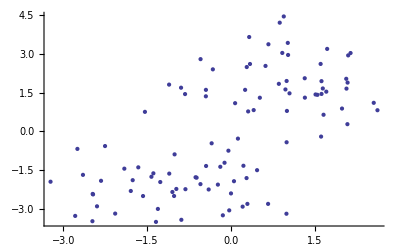

```mathematica
ListPlot[sample]
```

```mathematica
tmp=Join[t1,t2];
tg=Join[Table[{1,0},{Length[t1]}],Table[{0,1},{Length[t2]}]];
pg=KNN[sample,tmp,tg,K->4];
```

```mathematica
Total[tg]
```

{5,5}

```mathematica
(*nf=Nearest[tmp->tg,DistanceFunction->EuclideanDistance];*)
(*Commonest[nf[sample[[1]],6]]*)
ConstantArray[0,{Length[sample],Length[2]}];
```

```mathematica
tgs=Join[Table[{1,0},{50}],Table[{0,1},{50}]];
```

```mathematica
HammingDistance[Flatten[tgs],Flatten[pg]]/Length[pg]
```

1/50